```mathematica
(2 √6(((1-Exp[(-3/2)L*(m+1)])/(1-Exp[(-3/2)L]))-1/2))/((1-Exp[-L(m+1)])/(1-Exp[-L])-1/2)^(3/2)//Expand
```

```mathematica
-(√6)/((-1/2+(1-ⅇ^(-L (1+m)))/(1-ⅇ^-L))^(3/2))+(2 √6)/((1-ⅇ^(-3 L/2)) (-1/2+(1-ⅇ^(-L (1+m)))/(1-ⅇ^-L))^(3/2))-(2 √6 ⅇ^(-3/2 L (1+m)))/((1-ⅇ^(-3 L/2)) (-1/2+(1-ⅇ^(-L (1+m)))/(1-ⅇ^-L))^(3/2))//Simplify
```

(4 √3 ⅇ^(-3/2 L (1+m)) (1+ⅇ^(L/2)) (-2 ⅇ^(3 L/2)+ⅇ^(3/2 L (1+m))+ⅇ^(3/2 L (2+m))))/((-1+ⅇ^L) (1+ⅇ^(L/2)+ⅇ^L) ((ⅇ^(-L (1+m)) (-2 ⅇ^L+ⅇ^(L (1+m))+ⅇ^(L (2+m))))/(-1+ⅇ^L))^(3/2))

```mathematica
((1-Exp[(-3/2)L*(m+1)])/(1-Exp[(-3/2)L]))-1/2//Simplify
```

```mathematica
(2(1-ⅇ^(-3/2 L (1+m)))-(1-ⅇ^(-3 L/2)))/(2(1-ⅇ^(-3 L/2)))//Simplify
```

-(1+ⅇ^(3 L/2)-2 ⅇ^(-(3 L m)/2))/(2-2 ⅇ^(3 L/2))

```mathematica
(2(1-Exp[-L(m+1)])-(1-Exp[-L]))/(2(1-Exp[-L]))//Simplify
```

(ⅇ^(-L m) (-2+ⅇ^(L m)+ⅇ^(L (1+m))))/(2 (-1+ⅇ^L))

```mathematica
g[m_,L_,α_]:=(4 √3 ⅇ^(-3/2 L (1+m)) (1+ⅇ^(L/2)) (-2 ⅇ^(3 L/2)+ⅇ^(3/2 L (1+m))+ⅇ^(3/2 L (2+m))))/((-1+ⅇ^L) (1+ⅇ^(L/2)+ⅇ^L) ((ⅇ^(-L (1+m)) (-2 ⅇ^L+ⅇ^(L (1+m))+ⅇ^(L (2+m))))/(-1+ⅇ^L))^(3/2))
```

```mathematica
f[m_,L_,α_]:=(√6 ⅇ^(3/2 L (2+m)) (-1+ⅇ^(L/2))^2 (1+ⅇ^(L/2))^3 (-2+ⅇ^((3 L m)/2)+ⅇ^(3/2 L (1+m))))/((1+ⅇ^(L/2)+ⅇ^L) (-ⅇ^L+ⅇ^(L (1+m)))^3 α^(3/2))
```

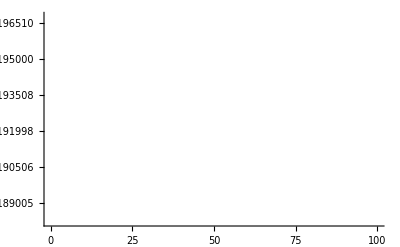

```mathematica
Plot[g[m,1.7,10^-5],{m,0,100}]
```